# BE/CS 196a Lab 12 Design and analysis of a DNA origami tile array that reconfigures from a sword to a rattlesnake

## CRN Simulator

Chemical Reaction Network (CRN) Simulator package is developed by David Soloveichik. Copyright 2009-2015. 
http://users.ece.utexas.edu/~soloveichik/crnsimulator.html

### Public interface specification

```mathematica
Notation`AutoLoadNotationPalette = False;
Needs["Notation`"]
BeginPackage["CRNSimulator`", {"Notation`"}];
```

```mathematica
rxn::usage="Represents an irreversible reaction. eg. rxn[a+b,c,1]";
revrxn::usage="Represents a reversible reaction. eg. revrxn[a+b,c,1,1]";
conc::usage="Initial concentration: conc[x,10] or conc[{x,y},10].";
term::usage="Represents an additive term in the ODE for species x. \
Species concentrations must be expressed in x[t] form. eg. term[x, -2 x[t]*y[t]]";
```

```mathematica
SimulateRxnsys::usage=
"SimulateRxnsys[rxnsys,endtime] simulates the reaction system rxnsys for time 0 \
to endtime. In rxnsys, initial concentrations are specified by conc statements. \
If no initial condition is set for a species, its initial concentration is set to 0. \
Rxnsys can also include term[] statements (e.g. term[x, -2 x[t]]) which are additively \
combined together with term[]s derived from rxn[] statements. \
Rxnsys can also include direct ODE definitions for some species (e.g. x'[t]==...), \
or direct definitions of species as functions of time (e.g. x[t]==...), \
which are passed to NDSolve without modification. \
Any options specified (eg WorkingPrecision->30) \
are passed to NDSolve."; 
SpeciesInRxnsys::usage=
"SpeciesInRxnsys[rxnsys] returns the species in reaction system rxnsys. \
SpeciesInRxnsys[rxnsys,pttrn] returns the species in reaction system rxnsys \
matching Mathematica pattern pttrn (eg x[1,_]).";
SpeciesInRxnsysStringPattern::usage=
"SpeciesInRxnsysPattern[rxnsys,pttrn] returns the species in reaction system rxnsys \
matching Mathematica string pattern pttrn. \
(Eg \"g$*\" matches all species names starting with \"g$\" ; \ 
can also do RegularExpression[\"o..d.\$.*\"].)";
RxnsysToOdesys::usage=
"RxnsysToOdesys[rxnsys,t] returns the ODEs corresponding to reaction system rxnsys, \
with initial conditions. If no initial condition is set for a species, its initial \
concentration is set to 0. \
The time variable is given as the second argument; if omitted it is set to Global`t.";
```

```mathematica
(*To use instead of Sequence in functions with Hold attribute but not HoldSequence,
like Module, If, etc*)
Seq:=Sequence
```

### Private

```mathematica
Begin["`Private`"];
```

```mathematica
Notation[ParsedBoxWrapper[RowBox[{"r_", " ", OverscriptBox["→", RowBox[{" ", "k_", " "}]], " ", "p_", " "}]] ⟺ ParsedBoxWrapper[RowBox[{"rxn", "[", RowBox[{"r_", ",", "p_", ",", "k_"}], "]"}]]]
Notation[ParsedBoxWrapper[RowBox[{"r_", " ", UnderoverscriptBox["⇄", "k2_", "k1_"], " ", "p_", " "}]] ⟺ ParsedBoxWrapper[RowBox[{"revrxn", "[", RowBox[{"r_", ",", "p_", ",", "k1_", ",", "k2_"}], "]"}]]]
AddInputAlias[ParsedBoxWrapper[RowBox[{"□", " ", OverscriptBox["→", RowBox[{" ", "□", " "}]], " ", "□", " "}]],"rxn"]
AddInputAlias[ParsedBoxWrapper[RowBox[{"□", " ", UnderoverscriptBox["⇄", "□", "□"], " ", "□", " "}]],"revrxn"]
```

```mathematica
(*We want rxn[a+b,c,1] to be different from rxn[b+a,c,1], so we have to set attribute
HoldAll. But we also want to evaluate if any variables can be evaluated.*)
SetAttributes[{rxn,revrxn}, HoldAll]
rxn[rs_Plus,ps_,k_]:=
 ReleaseHold[ReplacePart[rxn[1,ps,k],1->Hold[Plus]@@List@@Unevaluated[rs]]]/;
 Hold@@Unevaluated[rs] =!= Hold@@List@@Unevaluated[rs]
rxn[rs_,ps_Plus,k_]:=
 ReleaseHold[ReplacePart[rxn[rs,1,k],2->Hold[Plus]@@List@@Unevaluated[ps]]]/;
 Hold@@Unevaluated[ps] =!= Hold@@List@@Unevaluated[ps]
rxn[rs_,ps_,k_]:=
 (With[{rse=rs},rxn[rse,ps,k]])/;Head[rs]=!=Plus&&Unevaluated[rs]=!=rs
rxn[rs_,ps_,k_]:=
 (With[{pse=ps},rxn[rs,pse,k]])/;Head[ps]=!=Plus&&Unevaluated[ps]=!=ps
rxn[rs_,ps_,k_]:=
 (With[{ke=k},rxn[rs,ps,ke]])/;Unevaluated[k]=!=k
```

```mathematica
(* Automatically expand revrxn and concentration lists *)
revrxn[r_,p_,k1_,k2_]:=Sequence[rxn[r,p,k1],rxn[p,r,k2]]
conc[xs_List,c_]:=Seq@@(conc[#,c]&/@xs)

(* People are often confused about rxn[0,x,1] instead of rxn[1,x,1]. So we automatically replace any integer with 1. *)
rxn[Except[1,_Integer],ps_,k_]:=rxn[1,ps,k]
```

```mathematica
(* Species as products or reactants in rxn[] statements, as well as defined in x'[t]== or x[t]== statements \
or term statements, or conc statements *)
SpeciesInRxnsys[rxnsys_]:=
 Union[
 	Cases[Cases[rxnsys,rxn[r_,p_,_]:>Seq[r,p]]/.Times|Plus->Seq,s_Symbol|s_Symbol[__]],
 	Cases[rxnsys, x_'[_]==_ | x_[_]==_ | term[x_,__] | conc[x_,_] :> x]]
SpeciesInRxnsys[rsys_,pattern_]:=Cases[SpeciesInRxnsys[rsys],pattern]
SpeciesInRxnsysStringPattern[rsys_,pattern_]:=Select[SpeciesInRxnsys[rsys],StringMatchQ[ToString[#],pattern]&]
```

```mathematica
(* Check if a species' initial value is set in a odesys *) 	
InitialValueSetQ[odesys_,x_]:=
 MemberQ[odesys,x[_]==_]

(* Check if a species is missing an ODE or a direct definition (x[t]=_) in odesys. *)
MissingODEQ[odesys_,x_,t_Symbol]:=
 !MemberQ[odesys, D[x[t],t]==_ | x[t]==_]  	

RxnsysToOdesys[rxnsys_,t_Symbol:Global`t]:=
 Module[
  {spcs=SpeciesInRxnsys[rxnsys], concs, termssys, odesys, eqsFromTerms, eqsFromConcs},

  (* extract conc statements and sum them for same species *)
  concs = conc[#[[1,1]],Total[#[[;;,2]]]]&/@GatherBy[Cases[rxnsys,conc[__]],Extract[{1}]];

  (* Convert rxn[] to term[] statements *)
  termssys=rxnsys /. rxn:rxn[__]:>Seq@@ProcessRxnToTerms[rxn,t];

  (* ODEs from parsing terms *)
  eqsFromTerms = ProcessTermsToOdes[Cases[termssys,term[__]],t]; 
  (* initial values from parsing conc statements *)
  eqsFromConcs = Cases[concs,conc[x_,c_]:>x[0]==c]; 

  (* Remove term and conc statements from rxnsys and add eqs generated from them. 
     If there is a conflict, use pass-through equations *)
  odesys = DeleteCases[termssys, term[__]|conc[__]];
  odesys = Join[odesys,
                DeleteCases[eqsFromTerms, Alternatives@@(#'[t]==_& /@ Cases[odesys,(x_'[t]|x_[t])==_:>x])],
                eqsFromConcs];
     
  (* For species still without initial values, add zeros *)
  odesys = Join[odesys, #[0]==0& /@ Select[spcs, !InitialValueSetQ[odesys,#]&]];

  (* For species still without ODE or direct definition, add zero time derivative *)
  (* This can happen for example if conc is defined, but nothing else *)
  Join[odesys, D[#[t],t]==0& /@ Select[spcs, MissingODEQ[odesys,#,t]&]]
 ]
 
(* Create list of ODEs from parsing term statements. terms should be list of term[] statements. *) 
ProcessTermsToOdes[terms_,t_Symbol]:=
Module[{spcs=Union[Cases[terms,term[s_,_]:>s]]},
#'[t]==Total[Cases[terms,term[#,rate_]:>rate]] & /@ spcs];

(* Create list of term[] statements from parsing a rxn statement *) 
ProcessRxnToTerms[reaction:rxn[r_,p_,k_],t_Symbol]:=
Module[{spcs=SpeciesInRxnsys[{reaction}], rrate, spccoeffs,terms},
(* compute rate of this reaction *)
rrate = k (r/.{Times[b_,s_]:>s^b,Plus->Times});
(*for each species, get a net coefficient*)
spccoeffs=Coefficient[p-r,#]& /@ spcs;
(*create term for each species*)
terms=MapThread[term[#1,#2*rrate]&,{spcs, spccoeffs}];
(*change all species variables in the second arg in term[] to be functions of t*)
terms/.term[spc_,rate_]:>term[spc,rate/.s_/;MemberQ[spcs,s]:>s[t]]];
```

```mathematica
SimulateRxnsys[rxnsys_,endtime_,opts:OptionsPattern[NDSolve]]:=
 Module[{spcs=SpeciesInRxnsys[rxnsys],odesys=RxnsysToOdesys[rxnsys,Global`t]},
 Quiet[NDSolve[odesys, spcs, {Global`t,0,endtime},opts,MaxSteps->Infinity,AccuracyGoal->MachinePrecision],{NDSolve::"precw"}][[1]]]
```

```mathematica
End[];
EndPackage[];
```

## Polymer CRNs

listToSpeciesName converts a polymer stored as a list of monomers to a species name that joins all monomers.

```mathematica
listToSpeciesName[list_]:=ToExpression[StringJoin[Table[ToString[list[[i]]],{i,Length[list]}]]]
```

polymerCRN generates a list of polymers and a list of polymer reactions based on a list of monomers, a list of rules for how the monomers interact with each other (each rule is defined as a pair of monomers with an order that applies to all rules, e.g. left to right, bottom to top), a list of rates of monomer interactions (one for each rule), and the maximum length of polymers enumerated (maxlength). 

Note: An experimental system will not have a set maximum length of polymers, and polymers could grow infinitely (whether it is likely or not depends on parameters including concentrations and rates). Setting a maximum length in simulation allows for the approximate modeling of an infinite chemical reaction network. The choice of the maximum length will affect the result of simulation (i.e. how accurate the approximation is). To understand the expected behavior of an experimental system, a good choice of the maximum length is just large enough so that no significant change in the result is observed with a larger number.

```mathematica
polymerCRN[monomers_,rules_,rates_,maxlength_]:=Module[{polymers,rxnsys,n1,n2,m,i,j,k,p,q,ruleset,newpolymer,newrxn},
polymers=Table[{{monomers[[i]]}},{i,Length[monomers]}];
rxnsys={};
n1=0;n2=0;m=1;
While[n1<n2 || m==1,
n1=n2;m++;
For[i=1,i≤Length[polymers],i++,
For[j=1,j≤Length[polymers[[i]]],j++,
ruleset=Position[rules[[;;,1]],polymers[[i,j,-1]]];
For[k=1,k≤Length[ruleset],k++,
p=Position[polymers[[;;,1,1]],rules[[ruleset[[k,1]],2]]][[1,1]];
For[q=1,q≤Length[polymers[[p]]],q++,
newpolymer=Join[polymers[[i,j]],polymers[[p,q]]];
newrxn=rxn[listToSpeciesName[polymers[[i,j]]]+listToSpeciesName[polymers[[p,q]]],listToSpeciesName[newpolymer],rates[[ruleset[[k,1]]]]];
If[FreeQ[polymers[[i]],newpolymer] && Length[newpolymer]≤maxlength,AppendTo[polymers[[i]],newpolymer]];
If[FreeQ[rxnsys,newrxn] && Length[newpolymer]≤maxlength,AppendTo[rxnsys,newrxn];
n2++]
]]]]];
{Table[listToSpeciesName[polymers[[i,j]]],{i,Length[polymers]},{j,Length[polymers[[i]]]}]//Flatten,
rxnsys}]
```

## Plot function

PlotSim function plots a simulation including multiple trajectories.
SIMcircuit is a simulation.
SIMtime is the simulation time.  
trajectories is a list of species names or concentrations shown in the legend. The default is none.
TrajectoryLabel is a label for the legend of trajectories. The default is none.
OutputLabel is a label for the vertical axis, which should be a description of the output simulated, with unit specified. The default is none.
CircuitLabel is a label for the plot. It can be a description of the circuit. The default is none. 
TimeRange defines the range of time plotted. The unit is hours. The format is All, {All, max}, {min, All}, or {min, max}, where min and max should be given as the desired numbers for a time range. The default is All (i.e. all data points plotted).
OutputRange defines the range of output plotted. The unit is nM. Same format and default as timeRange.

```mathematica
Options[PlotSim]={plotSize->300,labelSize->16,lineThickness->2};
PlotSim[SIMcircuit_,SIMtime_,trajectories_:"",TrajectoryLabel_:"",OutputLable_:"",CircuitLabel_:"",TimeRange_:All,OutputRange_:All,OptionsPattern[]]:=
Plot[SIMcircuit,{t,0,SIMtime},PlotLabel->Style[CircuitLabel,OptionValue[labelSize]],
Frame->True,FrameLabel->{"Time (hours)",OutputLable},
PlotStyle->Table[{AbsoluteThickness[OptionValue[lineThickness]],ColorData["Rainbow"][i]},{i,If[Length[SIMcircuit]<8,0.12,0],0.96,0.96/Length[SIMcircuit]}],
PlotLegends->Placed[SwatchLegend[Automatic,trajectories,LegendLabel->TrajectoryLabel,LegendMarkerSize->OptionValue[labelSize]*0.75],Right],
LabelStyle->Directive[Gray,FontSize->OptionValue[labelSize],FontFamily->"Helvetica"],
GridLines->Automatic,
PlotRange->{TimeRange,OutputRange},AspectRatio->1/1.3,ImageSize->OptionValue[plotSize]]
```

## Simulation (an example polymer reaction)

Remove the tail connector and make the tail have a blue receive instead of a dark green receive
With the revised set of tiles, we would get any number of unique structures.
-Graphics-
-Graphics-

Use polymerCRN defined above under Polymer CRNs to enumerate polymer reactions given a set of monomers and their interactions. (Note: the maxlength below is chosen to demonstrate a simple simulation, see explanation under Polymer CRNs to make your own choice about the set maximum length of polymers.)

```mathematica
monomers={a,b,c};
rules={{a,b},{b,a},{a,c}};
k=2*10^6; (* rate of hybridization, unit: /M/s *)
rates={k,k,k};
maxlength=6;
{polymers,rxnsys}=polymerCRN[monomers,rules,rates,maxlength];
```

```mathematica
polymers
```

{a,ab,ac,aba,abab,abac,ababa,ababab,ababac,b,ba,bab,bac,baba,babab,babac,bababa,c}

```mathematica
rxnsys
```

{a+b →^2000000 ab ,a+c →^2000000 ac ,ab+a →^2000000 aba ,2 ab →^2000000 abab ,ab+ac →^2000000 abac ,ab+aba →^2000000 ababa ,ab+abab →^2000000 ababab ,ab+abac →^2000000 ababac ,aba+b →^2000000 abab ,aba+c →^2000000 abac ,abab+a →^2000000 ababa ,abab+ab →^2000000 ababab ,abab+ac →^2000000 ababac ,ababa+b →^2000000 ababab ,ababa+c →^2000000 ababac ,b+a →^2000000 ba ,b+ab →^2000000 bab ,b+ac →^2000000 bac ,b+aba →^2000000 baba ,b+abab →^2000000 babab ,b+abac →^2000000 babac ,b+ababa →^2000000 bababa ,ba+b →^2000000 bab ,2 ba →^2000000 baba ,ba+bab →^2000000 babab ,ba+bac →^2000000 babac ,ba+baba →^2000000 bababa ,ba+c →^2000000 bac ,bab+a →^2000000 baba ,bab+ab →^2000000 babab ,bab+ac →^2000000 babac ,bab+aba →^2000000 bababa ,baba+b →^2000000 babab ,baba+ba →^2000000 bababa ,baba+c →^2000000 babac ,babab+a →^2000000 bababa ,a+ba →^2000000 aba ,a+bab →^2000000 abab ,a+bac →^2000000 abac ,a+baba →^2000000 ababa ,a+babab →^2000000 ababab ,a+babac →^2000000 ababac ,aba+ba →^2000000 ababa ,aba+bab →^2000000 ababab ,aba+bac →^2000000 ababac }

Simulate the polymer reactions given initial concentrations of the monomers.

```mathematica
SIMtime=2; (* unit: hours *)
sc=10*10^-9; (* standard concentration, unit: M *)
polymersys={
rxnsys,
conc[a,2.5*sc],
conc[b,1*sc],
conc[c,1.5*sc]
}//Flatten;
sol=SimulateRxnsys[polymersys,SIMtime*60*60];
SIMpolymer=Table[polymers[[i]][t*60*60]/10^-9/.sol,{i,Length[polymers]}];
```

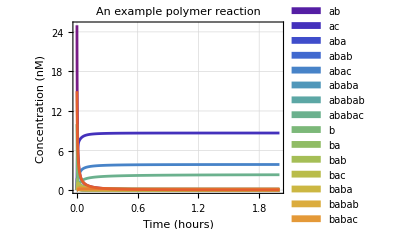

```mathematica
trajectories=polymers;
TrajectoryLabel="";
OutputLabel="Concentration (nM)"; 
CircuitLabel="An example polymer reaction";  
TimeRange={All,1};
PlotSim[SIMpolymer,SIMtime,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel,TimeRange]
```

Display final concentrations of polymers above a set threshold.

```mathematica
SIMpolymerFinal=Table[polymers[[i]][SIMtime*60*60]/10^-9/.sol,{i,Length[polymers]}];
threshold=0.1; (* threshold concentration, unit: nM *)
polymerThresholded=Position[SIMpolymerFinal,x_/;x>=threshold]//Flatten;
```

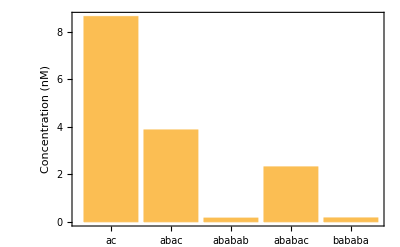

```mathematica
BarChart[SIMpolymerFinal[[polymerThresholded]],ChartLabels->Placed[polymers[[polymerThresholded]],Axis,Rotate[#,Pi/4]&],
Frame->True,FrameLabel->Style["Concentration (nM)",16]]
```

Display kinetics trajectories of polymers whose final concentrations are above a set threshold.

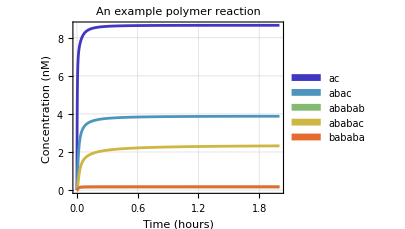

```mathematica
trajectories=polymers[[polymerThresholded]];
TrajectoryLabel="";
OutputLabel="Concentration (nM)"; 
CircuitLabel="An example polymer reaction";  
TimeRange={All,1};
PlotSim[SIMpolymer[[polymerThresholded]],SIMtime,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel,TimeRange]
```

Display final concentrations of polymers based on their lengths. (Note: the code assumes that all monomer names have the same number of characters.)

```mathematica
polymerBinned=ConstantArray[0,maxlength];
For[i=1,i<=Length[polymers],i++,
polymerBinned[[StringLength[ToString[polymers[[i]]]]/StringLength[ToString[monomers[[1]]]]]]+=polymers[[i]][SIMtime*60*60]/10^-9/.sol];
```

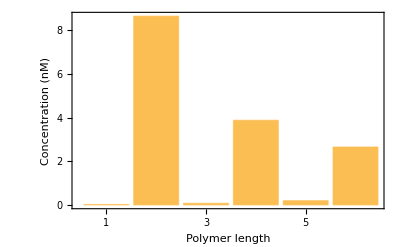

```mathematica
BarChart[polymerBinned,ChartLabels->Range[maxlength],
Frame->True,FrameLabel->{Style["Polymer length",16],Style["Concentration (nM)",16]}]
```

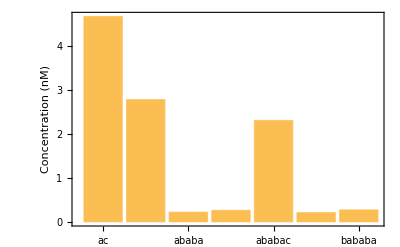
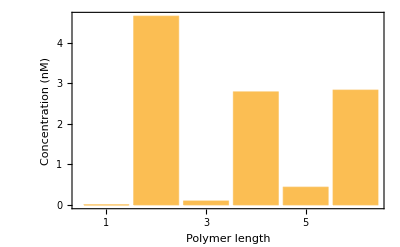
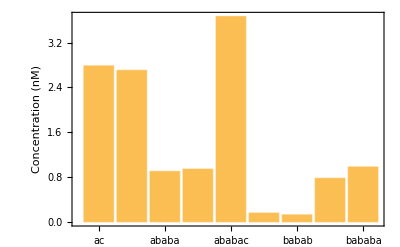
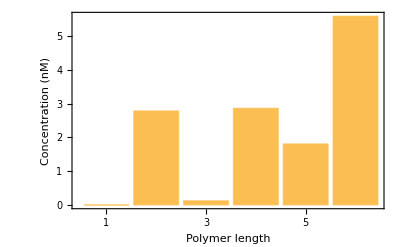
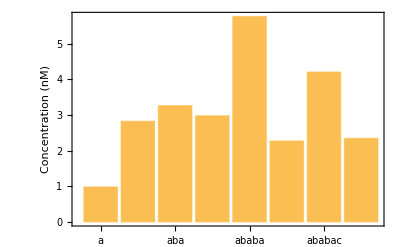
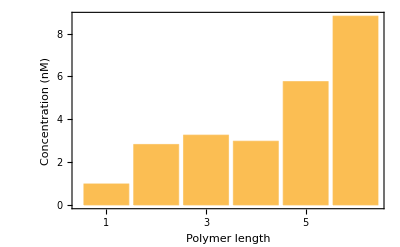
-Graphics-,-Graphics-: a,b,c:2,1,1
-Graphics-,-Graphics-: 
a,b,c:3,2,1
Increasing the concentration of both tiles ‘a’ and ‘b’ relative to tile ‘c’ will result in longer polymers. Keeping tile ‘a’ at a larger concentration relative to tile ‘b’ will result in a higher fraction of polymers with tile ‘a’ on one end that can displace the blade of the sword.
-Graphics-,-Graphics-: 
a,b,c:6,4,1
We can make the polymers that start with tile ‘a’ and end with tile ‘c’ increase with concentration, but adding a much higher concentration of tiles ‘a’ and ‘b’ relative to tile ‘c’. This makes sense because a lack of tile ‘c’ will cause strands to be able to keep extending, encouraging longer strands over shorter ones. 

-Graphics-
a,b,c:2.5,1,1.5
If we want a higher yield of polymers of length around 4 (‘abac’), we would want to choose relative concentrations of a,b,c to be 2.5,1,1.5 or to make up 25,10,15 of the 50 nm, respectively.


There will be 6 unique type of 2 by 2 array that will be created (0 pairs of eyes, 1 pair of eyes, 2 x 2 pairs of eyes, 3 pairs of eyes, 4 pairs of eyes).
-Graphics-